```mathematica
goldData=Import["/Users/benxgh1996/Desktop/Rutherford/data.xlsx",{"Data",1,Range[2,14],{1,2}}]
```

{{-15.,584.},{-12.5,661.},{-10.,680.},{-7.5,582.},{-5.,396.},{-2.5,273.},{0.,185.},{2.5,95.},{5.,41.},{7.5,22.8},{10.,13.8},{15.,2.55},{30.,0.493146}}

```mathematica
Length[goldData]
```

```mathematica
goldDataLog=goldData
```

{{-15.,584.},{-12.5,661.},{-10.,680.},{-7.5,582.},{-5.,396.},{-2.5,273.},{0.,185.},{2.5,95.},{5.,41.},{7.5,22.8},{10.,13.8},{15.,2.55},{30.,0.493146}}

```mathematica
For[i=1,i<=Length[goldDataLog],i++,goldDataLog[[i]][[2]]=Log[goldDataLog[[i]][[2]]]]
```

```mathematica
goldDataLog
```

{{-15.,6.3699},{-12.5,6.49375},{-10.,6.52209},{-7.5,6.36647},{-5.,5.98141},{-2.5,5.60947},{0.,5.22036},{2.5,4.55388},{5.,3.71357},{7.5,3.12676},{10.,2.62467},{15.,0.936093},{30.,-0.70695}}

```mathematica
FindFit[goldData,Log[k/Sin[1/2(θ-θ0) *(2π)/360]^4],{k,θ0},θ]
```

{k→1.89306×10^-6,θ0→1.14912}

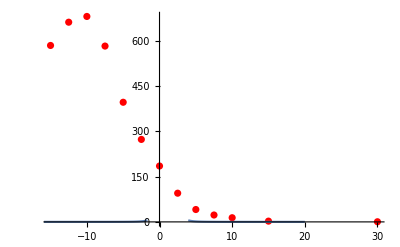

```mathematica
Show[ListPlot[goldData,PlotStyle->Red],Plot[k/Sin[1/2(θ-θ0) *(2π)/360]^4/.{k->1.8930613964971008*^-6,θ0->1.149119636874558},{θ,-20,20}]]
```

```mathematica
gold3Data=Import["/Users/benxgh1996/Desktop/Rutherford/data.xlsx",{"Data",2,Range[2,15],{1,2}}]
```

{{-15.,166.5},{-12.5,265.},{-10.,366.},{-7.5,585.},{-5.,761.},{-2.5,754.5},{0.,745.},{2.5,655.},{5.,464.},{7.5,318.},{10.,201.},{12.5,103.},{15.,72.5},{20.,21.6}}

```mathematica
gold3LogData = gold3Data
```

{{-15.,166.5},{-12.5,265.},{-10.,366.},{-7.5,585.},{-5.,761.},{-2.5,754.5},{0.,745.},{2.5,655.},{5.,464.},{7.5,318.},{10.,201.},{12.5,103.},{15.,72.5},{20.,21.6}}

```mathematica
For[i=1,i<=Length[gold3LogData],i++,
gold3LogData[[i]][[2]]=Log[gold3LogData[[i]][[2]]]]
```

```mathematica
gold3LogData
```

{{-15.,5.115},{-12.5,5.57973},{-10.,5.90263},{-7.5,6.37161},{-5.,6.63463},{-2.5,6.62606},{0.,6.61338},{2.5,6.48464},{5.,6.13988},{7.5,5.76205},{10.,5.3033},{12.5,4.63473},{15.,4.28359},{20.,3.07269}}

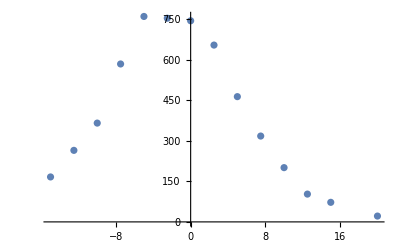

```mathematica
ListPlot[gold3Data]
```

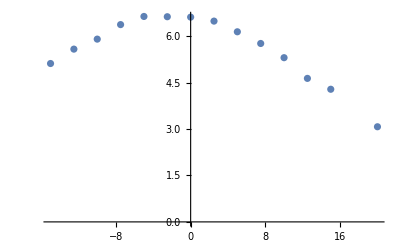

```mathematica
ListPlot[gold3LogData]
```

```mathematica
gold3LogDataCopy=Delete[gold3LogData,6]
```

{{-15.,5.115},{-12.5,5.57973},{-10.,5.90263},{-7.5,6.37161},{-5.,6.63463},{0.,6.61338},{2.5,6.48464},{5.,6.13988},{7.5,5.76205},{10.,5.3033},{12.5,4.63473},{15.,4.28359},{20.,3.07269}}

```mathematica
For[i=1,i<=Length[gold3LogDataCopy],i++,
gold3LogDataCopy[[i]][[2]]=Log[gold3LogDataCopy[[i]][[2]]]]
```

```mathematica
gold3LogDataCopy
```

{{-15.,1.63218},{-12.5,1.71914},{-10.,1.7754},{-7.5,1.85185},{-5.,1.8923},{0.,1.8891},{2.5,1.86944},{5.,1.81481},{7.5,1.75129},{10.,1.66833},{12.5,1.53358},{15.,1.45479},{20.,1.12255}}

```mathematica
FindFit[gold3LogDataCopy,Log[Log[k/Sin[1/2(θ-θ0) *(2π)/360]^4]],{k,θ0},θ]
```

FindFit::nrlnum: The function value {0.676277+0.317635 ⅈ,0.651644+0.297832 ⅈ,0.666299+0.276884 ⅈ,0.673229+0.254219 ⅈ,0.736353+0.228735 ⅈ,1.16076+0.149359 ⅈ,1.07982+«20» ⅈ,0.91539+0.206313 ⅈ,0.848835+0.235478 ⅈ,0.834391+0.2601 ⅈ,0.889393+0.28226 ⅈ,0.899695+0.30288 ⅈ,1.11669+0.341289 ⅈ} is not a list of real numbers with dimensions {13} at {k,θ0} = {-5.21681,0.937131}.

{k→-5.21681,θ0→0.937131}

```mathematica
gold3Data
```

{{-15.,166.5},{-12.5,265.},{-10.,366.},{-7.5,585.},{-5.,761.},{-2.5,754.5},{0.,745.},{2.5,655.},{5.,464.},{7.5,318.},{10.,201.},{12.5,103.},{15.,72.5},{20.,21.6}}

```mathematica
k/Sin[1/2(θ-θ0) *(2π)/360]^4/.{k->0.028234433742527047,θ0->-2.5,θ->}
```

4.60477

```mathematica
(201/60.44064173529479)*0.008490086041945252
```

0.0282344

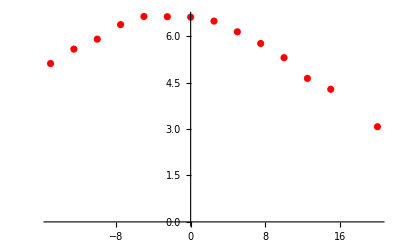

```mathematica
Show[ListPlot[gold3LogData,PlotStyle->Red],Plot[Log[k/Sin[1/2(θ-θ0) *(2π)/360]^4]/.{k->-4.644320315694722,θ0->1.414637269110715},{θ,-20,20}]]
```

```mathematica
k/Sin[1/2(θ-θ0) *(2π)/360]^4/.{k->-4.644320315694722,θ0->1.414637269110715,θ-> 5}
```

-4.84935×10^6

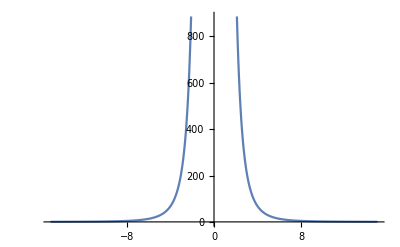

```mathematica
Plot[0.0001/Sin[1/2 x*(2π)/360]^4,{x,-15,15}]
```

```mathematica
b={1,2,3}
```

{1,2,3}

```mathematica
Delete[b,1]
```

{2,3}

```mathematica
b
```

{1,2,3}

```mathematica
Delete[b,2]
```

{1,3}

```mathematica
FindFit[gold3LogData,Log[k/Sin[1/2(θ-θ0) *(2π)/360]^4],{k,θ0},θ]
```

FindFit::nrlnum: The function value {4.20714+3.14159 ⅈ,4.39948+3.14159 ⅈ,4.86554+3.14159 ⅈ,5.38279+3.14159 ⅈ,6.43427+3.14159 ⅈ,8.41697+3.14159 ⅈ,12.5004+3.14159 ⅈ,«19»+«18» ⅈ,9.25447+3.14159 ⅈ,7.51743+3.14159 ⅈ,6.60134+3.14159 ⅈ,6.25015+3.14159 ⅈ,5.79096+3.14159 ⅈ,5.7565+3.14159 ⅈ} is not a list of real numbers with dimensions {14} at {k,θ0} = {-4.64432,1.41464}.

{k→-4.64432,θ0→1.41464}

```mathematica
gold3LogData//ListPlot[#,Joined->True]&
```

```mathematica
Manipulate[Show[ListPlot[gold3Data,ScalingFunctions->"Log"],Plot[Log[k/Sin[1/2(θ-θ0) (2π)/360]^4],{θ,-15,15}]],{k,.0001,1},{θ0,-5,0}]
```

ListPlot::lpn: gold3Data is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[gold3Data,ScalingFunctions→Log],].

```mathematica
FindFit[gold3LogData,{Log[k/Sin[1/2(θ-θ0) *(2π)/360]^4],{k>0,θ0<0}},{k,θ0},θ]
```

{k→30.2661,θ0→-70.0602}

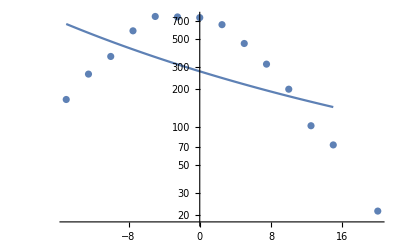

```mathematica
Show[ListPlot[gold3Data,ScalingFunctions->"Log"],Plot[Log[k/Sin[1/2(θ-θ0) (2π)/360]^4]/.%139,{θ,-15,15}]]
```

```mathematica
g3dc=Select[gold3Data,Abs[First@#]>7.5&]
```

{{-15.,166.5},{-12.5,265.},{-10.,366.},{10.,201.},{12.5,103.},{15.,72.5},{20.,21.6}}

```mathematica
Manipulate[g3dc=Select[gold3Data,Abs[First@#]>i&]//MatrixForm,{i,0,15}]
```

Select::normal: Nonatomic expression expected at position 1 in Select[gold3Data,Abs[First[#1]]>FE`i$$12&].

```mathematica
g3dc//MatrixForm
```

(-15. | 166.5
-12.5 | 265.
-10. | 366.
10. | 201.
12.5 | 103.
15. | 72.5
20. | 21.6)

```mathematica
MatrixForm@gold3Data
```

(-15. | 166.5
-12.5 | 265.
-10. | 366.
-7.5 | 585.
-5. | 761.
-2.5 | 754.5
0. | 745.
2.5 | 655.
5. | 464.
7.5 | 318.
10. | 201.
12.5 | 103.
15. | 72.5
20. | 21.6)

```mathematica
Manipulate[Show[ListPlot[g3dc,ScalingFunctions->"Log"],Plot[Log[k/Sin[1/2(θ-θ0) (2π)/360]^4],{θ,-15,15}]],{k,.0001,1},{θ0,-5,0}]
```

ListPlot::lpn: (20. | 21.6) is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[(20. | 21.6),ScalingFunctions→Log],].

ListPlot::lpn: Select[gold3Data,Abs[First[#1]]>FE`i$$12&] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Select[gold3Data,Abs[First[«1»]]>FE`i$$12&],ScalingFunctions→Log],].

ListPlot::lpn: Select[gold3Data,Abs[First[#1]]>FE`i$$4&] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Select[gold3Data,Abs[First[«1»]]>FE`i$$4&],ScalingFunctions→Log],].

```mathematica
FindFit[{First@#,Log@Last@#}&/@g3dc,{Log[k/Sin[1/2(θ-θ0) *(2π)/360]^4],{k>0,θ0<0}},{{k,.02},θ0},θ]
```

{k→0.0225245,θ0→-1.09334}

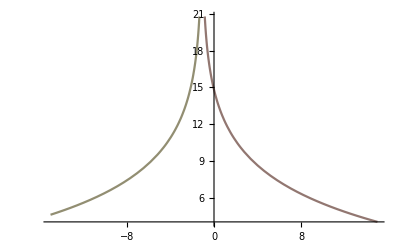

```mathematica
Plot[Log[k/Sin[1/2(θ-θ0) (2π)/360]^4]/.%148,{θ,-15,15},ColorFunction->"Rainbow"]
```

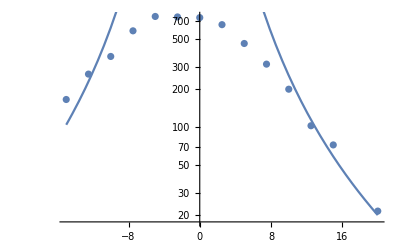

```mathematica
Show[ListPlot[gold3Data,ScalingFunctions->"Log"],Plot[Log[k/Sin[1/2(θ-θ0) (2π)/360]^4]/.%148,{θ,-15,20}]]
```

```mathematica
NonlinearModelFit
```

```mathematica
Module[
```

```mathematica
Compile[
```

```mathematica
{1/2*Quantile[ChiSquareDistribution[2k],α/2],1/2*Quantile[ChiSquareDistribution[2k+2],1-α/2]}/.{α-> 0.1,k-> 100}
```

{84.1393,118.079}

```mathematica
{(1/2*Quantile[ChiSquareDistribution[2k],α/2]-k)/√k,(1/2*Quantile[ChiSquareDistribution[2k+2],1-α/2]-k)/√k}/.{α-> 0.32,k-> 100000000000}
```

{-0.994458,0.994528}